```mathematica
Clear["Global`*"]
```

```mathematica
(* Mean frequencies of good individuals *)
gxgood=(1-gx)*ϵ;
gxbad=gx*(1-ϵ);
gygood=(1-gy)*e;
gybad=gy*(1-e);
gzgood=x*(1-gz)*(gx*ϵ+(1-gx)*e)+y*(1-gz)*(gy*ϵ+(1-gy)*e)+z*(1-gz)*(gz*ϵ+(1-gz)*e);
gzbad=x*gz*(gx*(1-ϵ)+(1-gx)*(1-e))+y*gz*(gy*(1-ϵ)+(1-gy)*(1-e))+z*gz*(gz*(1-ϵ)+(1-gz)*(1-e));
(*g=fx*gx+fy*gy+fz*gz;
g2=fx*gx^2+fy*gy^2+fz*gz^2;
b2=1-2*g+g2;
d2=g-g2;
ϵ=(1-e1)*(1-e2)+e1*e2;*)
```

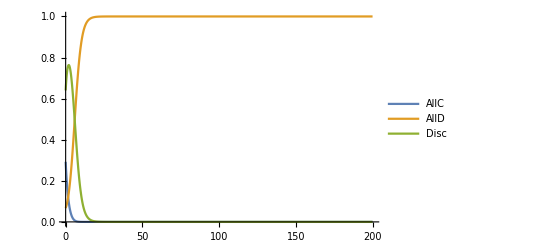

```mathematica
(* Plot numerical solutions *)
e=0.45;
ϵ=0.45;
γ=1;
r=3;
Px=r*(x[t]+(1-x[t]-y[t])*gx[t])-1;
Py=r*(x[t]+(1-x[t]-y[t])*gy[t]);
Pz=r*(x[t]+(1-x[t]-y[t])*gz[t])-g;
Pbar=x[t]*Px+y[t]*Py+(1-x[t]-y[t])*Pz;
Δgx=gxgood-gxbad/.{gx->gx[t]};
Δgy=gygood-gybad/.{gy->gy[t]};
Δgz=gzgood-gzbad/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]};
z=1-x[t]-y[t];
g=x[t]*gx[t]+y[t]*gy[t]+(1-x[t]-y[t])*gz[t];
r1=RandomReal[];
r2=RandomReal[];
r3=RandomReal[];
x0=r1/(r1+r2+r3);
y0=r2/(r1+r2+r3);
gx0=RandomReal[];
gy0=RandomReal[];
gz0=RandomReal[];
sol=NDSolve[{x'[t]==x[t]*(Px-Pbar),y'[t]==y[t]*(Py-Pbar),gx'[t]== γ*Δgx,gy'[t]==γ*Δgy,gz'[t]==γ*Δgz,x[0]==x0,y[0]==y0,gx[0]==gx0,gy[0]==gy0,gz[0]== gz0},{x,y,gx,gy,gz},{t,0,200}];
Plot[Evaluate[{x[t],y[t],1-x[t]-y[t]}/.sol],{t,0,200},PlotLegends->{"AllC","AllD","Disc"}]
```